# Benchmark Test

Run the test file

```mathematica
testRes = TestReport["Benchmark.nb"]
```

TestReportObject[…]

```mathematica
testRes["TestsFailed"]
```

<|TestsFailedWrongResults→<|3680030248505891463→TestObject[…]|>,TestsFailedWithMessages→<||>,TestsFailedWithErrors→<||>|>

Extract the inputs

```mathematica
testInputs=#["Input"]&/@Values[testRes["TestsSucceeded"]];
```

Destruct the equivalence checking into calculation of two examples, using the same environment.

```mathematica
DestructDiracEq[testexample_]:={
testexample/.{Verbatim[DNEqQ][A_,B_]:>DNNorm[A]},
testexample/.{Verbatim[DNEqQ][A_,B_]:>DNNorm[B]}
};
```

## Prepare the Examples

```mathematica
singleExamples=Flatten[Table[Flatten[DestructDiracEq/@testInputs],1]];
```

## Define the Example Evaluate Function

```mathematica
DiracCBHook[term_]:=(maxSize=Max[maxSize,LeafCount[term]];maxMemoryUsed=Max[maxMemoryUsed,MemoryInUse[]];term);
```

```mathematica
ExEvaluate[input_]:=Block[{startTime,endTime,initMemoryUsed=MemoryInUse[],maxMemoryUsed=MemoryInUse[],result,maxSize=0},
startTime=Now;
result=Evaluate[input];
endTime=Now;
(* Use DNNormWithHook to calculate the maximum leaf count and memory used *) 
ReleaseHold[Unevaluated[input][[1]]/.{DNNorm->DNNormWithHook}];
<|"Initial"->HoldForm[input],"Result"->result,"EvaluationTime"->endTime-startTime,"MaxMemoryUsed"->maxMemoryUsed-initMemoryUsed,"MaxSize"->maxSize|>]
```

## Apply the Evaluation and Monitor the Progress

```mathematica
EvalRes=Module[{i=0},
Monitor[
(With[{res=ExEvaluate[Unevaluated[ReleaseHold[#]]]},i++;res])&/@singleExamples,
ProgressIndicator[i/Length[singleExamples]]]
];
```

Sort according to maxsize.

```mathematica
EvalRes=Sort[EvalRes,#1["MaxSize"]<#2["MaxSize"]&]
```

```mathematica
Dataset[EvalRes]
```

### Manually Check the suitable examples

```mathematica
Manipulate[EvalRes[[i]],{i,1,Length[EvalRes],1}]
```

```mathematica
ReleaseHold[EvalRes[[229]]["Initial"]]
```

((0⊗_P0)+_O(1⊗_P1))

## Plot the Evaluation Result

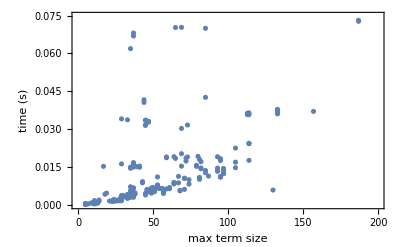

```mathematica
timePlot=ListPlot[
{#["MaxSize"],#["EvaluationTime"]}&/@EvalRes,
PlotRange->{{0, 200},Automatic},
(*PlotRange->All,*)
Frame->True,
FrameLabel->{"max term size","time (s)"}]
```

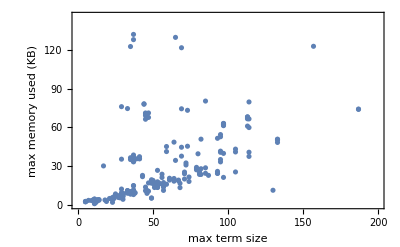

```mathematica
memPlot=ListPlot[
{#["MaxSize"],#["MaxMemoryUsed"]/1024}&/@EvalRes,
PlotRange->{{0, 200},Automatic},
Frame->True,
FrameLabel->{"max term size","max memory used (KB)"}
(*PlotLabel->"Evaluation Results"*)]
```

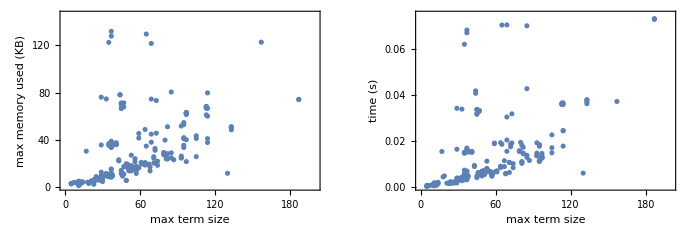

```mathematica
GraphicsGrid[{{memPlot,timePlot}}]
```

```mathematica
Rasterize[%105,"Image"]
```

-Graphics-